```mathematica
AppendTo[$Path, NotebookDirectory[]];
```

```mathematica
Get["CubeAcquire.wl"]
Get["CubeVisualize.wl"]
Get["CubeCore.wl"]
```

```mathematica
cubeString = sampleStrings["solved"]
```

WWWWWWWWWOOOGGGRRRBBBOOOGGGRRRBBBOOOGGGRRRBBBYYYYYYYYY

## 2D Cube

```mathematica
cube2D = Generate2DCube[cubeString];
```

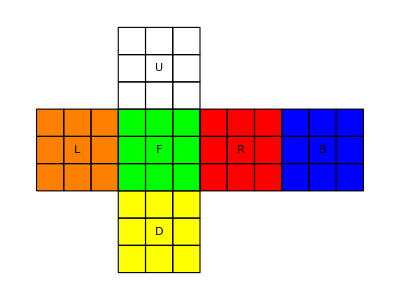

```mathematica
Visualize2DCube[cube2D];
```

## 3D Cube

```mathematica
cube3DPieces = GetPieces[cubeString];
```

```mathematica
cube3D = Dynamic[Generate3DCube[cube3DPieces]];
```

```mathematica
Visualize3DCube[cube3D];
```

-Graphics3D-

### Controlli

#### Generale

```mathematica
List[
Button["Load solved",cube3DPieces=GetPieces[sampleStrings["solved"]];],
Button["Load start",cube3DPieces=GetPieces[sampleStrings["start"]];]
]
```

{Load solved,Load start}

#### Mosse standard cubo

```mathematica
List[Button["L",cube3DPieces=RotateL[cube3DPieces];],Button["L'",cube3DPieces=RotateLi[cube3DPieces];],Button["R",cube3DPieces=RotateR[cube3DPieces];],Button["R'",cube3DPieces=RotateRi[cube3DPieces];],Button["U",cube3DPieces=RotateU[cube3DPieces];],Button["U'",cube3DPieces=RotateUi[cube3DPieces];],Button["D",cube3DPieces=RotateD[cube3DPieces];],Button["D'",cube3DPieces=RotateDi[cube3DPieces];],Button["F",cube3DPieces=RotateF[cube3DPieces];],Button["F'",cube3DPieces=RotateFi[cube3DPieces];],Button["B",cube3DPieces=RotateB[cube3DPieces];],Button["B'",cube3DPieces=RotateBi[cube3DPieces];]]
```

{L,L',R,R',U,U',D,D',F,F',B,B'}

#### Rotazione cubo

```mathematica
List[Button["X",cube3DPieces=RotateX[cube3DPieces];],Button["X'",cube3DPieces=RotateXi[cube3DPieces];],Button["Y",cube3DPieces=RotateY[cube3DPieces];],Button["Y'",cube3DPieces=RotateYi[cube3DPieces];],Button["Z",cube3DPieces=RotateZ[cube3DPieces];],Button["Z'",cube3DPieces=RotateZi[cube3DPieces];]]
```

{X,X',Y,Y',Z,Z'}

```mathematica
(* get cubes idxs *)
getCube[total_, element_] := (First[Position[total, element]]);
getPos[total_, elements_, pattern_]:=(
idxs=Flatten[
Position[
Table[
Flatten[
Cases[{elements[[t]]["pos"]},pattern]],{t,1,Length[elements]}],
pattern]];
 Return[
Flatten[
Table[
getCube[total, elements[[idxs[[t]]]]], {t,1,Length[idxs]}]
]]);
getCol[total_,elements_, pattern_] := (
idxs=Flatten[
Position[
Table[
Flatten[
Cases[{elements[[t]]["colors"]},pattern]],{t,1,Length[elements]}],
pattern]];
Return[
Flatten[
Table[
getCube[total, elements[[idxs[[t]]]]], {t,1,Length[idxs]}]
]]);

(* find edges with whites *)
numberOfNone=Table[Count[cube3DPieces[[t]]["colors"],None],{t,1,Length[cube3DPieces]}];
(* contains the idx of edges in the original list *)
idxOfEdges=Position[numberOfNone,1];
edges=Flatten[Table[cube3DPieces[[idxOfEdges[[t]]]],{t,1,Length[idxOfEdges]}]];
pattern={___,"W",___};
getCol[cube3DPieces, edges, pattern]
idxOfWhitesTmp=Position[Table[Flatten[Cases[{edges[[t]]["colors"]},pattern]],{t,1,Length[edges]}],pattern];
(*whiteEdges=Flatten[Table[edges[[idxOfWhitesTmp[[t]]]],{t,1,Length[idxOfWhitesTmp]}]];*)
idxOfWhites=Flatten[Table[idxOfEdges[[idxOfWhitesTmp[[t]]]],{t,1,Length[idxOfWhitesTmp]}]]
whites=Flatten[Table[cube3DPieces[[idxOfWhites[[t]]]],{t,1,Length[idxOfWhites]}]];
```

{7,8,9,18}

{7,8,9,18}

```mathematica
(* Find yellow center cube *)
patternYcenter={None,"Y",None};
yCenter=First[Position[Table[cube3DPieces[[t]]["colors"],{t,1,Length[cube3DPieces]}],patternYcenter]];
yCubeCenter = cube3DPieces[[yCenter]]
```

{<|pos→{0,1,0},colors→{None,Y,None}|>}